```mathematica
(* to run for LAPTOP *)
basepath = "/Users/saveriobocini/numerics_PhD";
FOLDERFLIPS=basepath~StringJoin~"/VCmatrices/FLIPS";
FOLDERCATS=basepath~StringJoin~"/VCmatrices/CATS";
```

```mathematica
(* to run for DESKTOP *)
basepath="/home/sbocini/Numerics_LabDesktop";
FOLDERFLIPS=basepath~StringJoin~"/VCmatrices/FLIPS";
FOLDERCATS=basepath~StringJoin~"/VCmatrices/CATS";
```

## Choose the state

### dual XX

```mathematica
L=160;
TIMES=Sort[{0.2,12.48,16.58,20.67,24.77,28.86,32.96,37.05,4.29,41.14,45.24,8.39}];
FILENAME="/quantum_transistor/standard/L"~StringJoin~ToString[L]~StringJoin~"_Jx0.7_Jy0.0_Jz0.0_h0.0_BondDim300_dt0.01";
```

### dual XXZ

```mathematica
L=160;
TIMES=Sort[{0.2,12.48,16.58,20.67,24.77,28.86,32.96,37.05,4.29,41.14,45.24,8.39}];
FILENAME="/quantum_transistor/standard/L"~StringJoin~ToString[L]~StringJoin~"_Jx0.7_Jy0.0_Jz0.0_h0.21_BondDim220_dt0.01";
```

### transistor nonint

```mathematica
L=160;
TIMES=Sort[{0.2,12.48,16.58,20.67,24.77,28.86,32.96,37.05,4.29,41.14,45.24,8.39}];
FILENAME="/quantum_transistor/standard/L"~StringJoin~ToString[L]~StringJoin~"_Jx0.7_Jy0.14_Jz0.0_h0.21_BondDim220_dt0.01";
```

```mathematica
L=100;
TIMES=Sort[{0.2,12.34,14.77,17.19,19.62,2.63,22.05,24.48,5.06,7.48,9.91}];
FILENAME="/quantum_transistor/standard/L"~StringJoin~ToString[L]~StringJoin~"_Jx0.7_Jy0.28_Jz0.0_h0.0_BondDim400_dt0.01";
```

### transistor full glory

```mathematica
L=100;
TIMES=Sort[{0.2,12.34,14.77,17.19,19.62,2.63,22.05,24.48,26.91,29.33,5.06,7.48}];
pathtomodel="/quantum_transistor/fullglory";
FILENAME=pathtomodel~StringJoin~"/L"~StringJoin~ToString[L]~StringJoin~"_J1_gamma0.5_w0.7_Delta0.0_Dz0.6_hz0.0_BondDim300_dt0.01";
```

### weird XX

```mathematica
L=70;
TIMES=Sort[{0.2,10.69,14.19,17.68,21.18,24.68,28.18,31.67,3.7,7.19}];
FILENAME="/XtimesXXpYYtimesX/withXX/L"~StringJoin~ToString[L]~StringJoin~"_resc1_alpha0.7_Delta0.5_BondDim500_dt0.01";
```

### longrange XXZ

```mathematica
L=110;
TIMES=Sort[{0.2,10.47,11.93,13.4,1.67,3.13,4.6,6.07,7.53,9.0001}];
FILENAME="/longrange/XXZ/n2_L"~StringJoin~ToString[L]~StringJoin~"_Jx0.25_Jz0.1_g0.22_BondDim460_dt0.01";
```

### XXZ

```mathematica
L=160;
TIMES=Sort[{0.2,12.13,16.11,20.09,24.07,28.04,32.02,4.18,8.16}];
FILENAME="/U1invariance/XXZ/L"~StringJoin~ToString[L]~StringJoin~"_J0.5_Delta0.25_BondDim300_dt0.01_1flips";
```

```mathematica
L=160;
TIMES=Sort[{0.2,12.13,16.11,20.09,24.07,28.04,32.02,4.18,8.16}];
FILENAME="/U1invariance/XXZ/L"~StringJoin~ToString[L]~StringJoin~"_J0.5_Delta0.25_BondDim300_dt0.01_2flips";
```

```mathematica
L=160;
TIMES=Sort[{0.2,12.13,16.11,20.09,24.07,28.04,32.02,4.18,8.16}];
FILENAME="/U1invariance/XXZ/L"~StringJoin~ToString[L]~StringJoin~"_J0.5_Delta0.25_BondDim300_dt0.01_3flips";
```

### XXZ nonintegrable

```mathematica
L=160;
TIMES=Sort[{0.2,12.13,16.11,20.09,24.07,28.04,32.02,4.18,8.16}];
FILENAME="/U1invariance/XXZ_nonint/L"~StringJoin~ToString[L]~StringJoin~"_J0.5_Delta0.25_BondDim200_dt0.01_1flips";
```

```mathematica
L=160;
TIMES=Sort[{0.2,12.13,16.11,20.09,24.07,28.04,32.02,4.18,8.16}];
FILENAME="/U1invariance/XXZ_nonint/L"~StringJoin~ToString[L]~StringJoin~"_J0.5_Delta0.25_BondDim200_dt0.01_2flips";
```

```mathematica
L=160;
TIMES=Sort[{0.2,12.13,16.11,20.09,24.07,28.04,32.02,4.18,8.16}];
FILENAME="/U1invariance/XXZ_nonint/L"~StringJoin~ToString[L]~StringJoin~"_J0.5_Delta0.25_BondDim200_dt0.01_3flips";
```

### weird with TRANS

```mathematica
L=80;
TIMES=Sort[{0.2,1.42,11.16,12.38,2.64,3.85,5.07,6.29,7.51,8.73,9.95}];
FILENAME="/XtimesXXpYYtimesX/withTRANS/L"~StringJoin~ToString[L]~StringJoin~"_Jx0.3_Jy0.12_h0.0_Delta0.0_Jw0.27_BondDim300_dt0.01";
```

## Magnetization

```mathematica
(* note that Sqrt[1-Matrice[[j,j]]] gives the absolute value of the expectation value of the Pauli matrices *)
magnprofileFLIPS={};
magnprofileCATS={};
For[n=1,n<=Length[TIMES],++n,
time=TIMES[[n]];
MatriceCATS=Import[FOLDERCATS~StringJoin~FILENAME~StringJoin~"_t"~StringJoin~ToString[time]~StringJoin~".csv"];
MatriceFLIPS=Import[FOLDERFLIPS~StringJoin~FILENAME~StringJoin~"_t"~StringJoin~ToString[time]~StringJoin~".csv"];
AppendTo[magnprofileFLIPS,Table[{j-2L,Sqrt[1-MatriceFLIPS[[j,j]]]},{j,1+2L,L+2L}]];
AppendTo[magnprofileCATS,Table[{j-2L,Sqrt[1-MatriceCATS[[j,j]]]},{j,1+2L,L+2L}]]
]
```

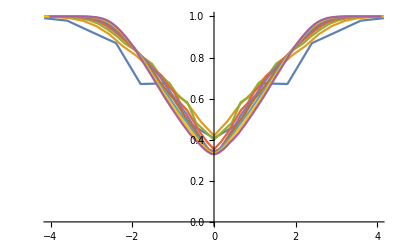

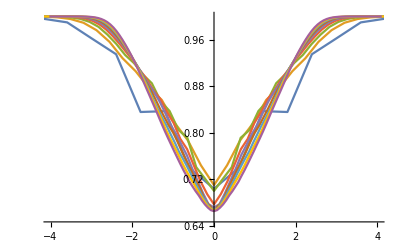

```mathematica
ListLinePlot[Table[{(#[[1]]-L/2)/TIMES[[n]],#[[2]]}&/@magnprofileFLIPS[[n]],{n,2,Length[TIMES]}],PlotRange->{{-4,4},All}]
ListLinePlot[Table[{(#[[1]]-L/2)/TIMES[[n]],#[[2]]}&/@magnprofileCATS[[n]],{n,2,Length[TIMES]}],PlotRange->{{-4,4},All}]
```

FittedModel[5.15788-4.92108 √x+2.8125 x]

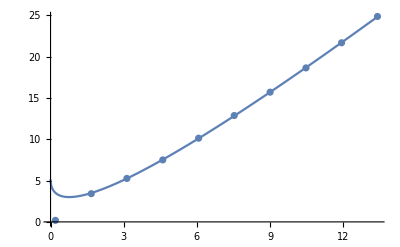

```mathematica
(* here we study the total magnetization and fit it with a function to see if it grows linearly or as a square root *)
lmFLIPS=LinearModelFit[Table[{TIMES[[n]],L-Total[magnprofileFLIPS[[n,All,2]]]},{n,3,Length[TIMES]}],{1,x,Sqrt[x]},x]
Show[ListPlot[Table[{TIMES[[n]],L-Total[magnprofileFLIPS[[n,All,2]]]},{n,Length[TIMES]}]],Plot[lmFLIPS[x],{x,0,TIMES[[-1]]}]]
```

FittedModel[2.50878-2.40039 √x+1.39388 x]

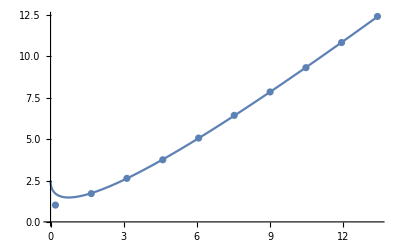

```mathematica
(* here we study the total magnetization and fit it with a function to see if it grows linearly or as a square root *)
lmCATS=LinearModelFit[Table[{TIMES[[n]],L-Total[magnprofileCATS[[n,All,2]]]},{n,3,Length[TIMES]}],{1,x,Sqrt[x]},x]
Show[ListPlot[Table[{TIMES[[n]],L-Total[magnprofileCATS[[n,All,2]]]},{n,Length[TIMES]}]],Plot[lmCATS[x],{x,0,TIMES[[-1]]}]]
```

## Lunghezza sottosistema

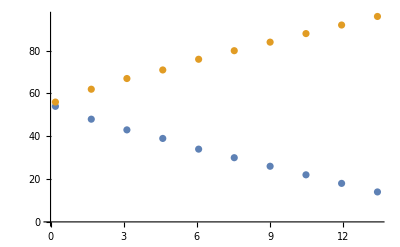

```mathematica
(*Lunghezza sottosistema*)
epsilon=0.001;
OmegaFLIPS={};
nmin=1;
For[n=1,n<=Length[TIMES],++n,
time=TIMES[[n]];
MatriceFLIPS=Import[FOLDERFLIPS~StringJoin~FILENAME~StringJoin~"_t"~StringJoin~ToString[time]~StringJoin~".csv"];
ellLFLIPS=1+Length[Select[FoldList[Times,1,Table[Sqrt[3-(MatriceFLIPS[[j,j]]+MatriceFLIPS[[j+L,j+L]]+MatriceFLIPS[[j+2L,j+2L]])],{j,1,L}]],#>1-epsilon&]];
ellRFLIPS=Length[MatriceFLIPS]/3-Length[Select[FoldList[Times,1,Reverse[Table[Sqrt[3-(MatriceFLIPS[[j,j]]+MatriceFLIPS[[j+L,j+L]]+MatriceFLIPS[[j+2L,j+2L]])],{j,1,L}]]],#>1-epsilon&]];
If[ellLFLIPS>ellRFLIPS, Print["Warning for ",n,": nmin has been updated to ", n+1]; nmin=n+1;];
AppendTo[OmegaFLIPS,{time,ellLFLIPS,ellRFLIPS}]
]
ListPlot[{OmegaFLIPS[[All,{1,2}]],OmegaFLIPS[[All,{1,3}]]}]
```

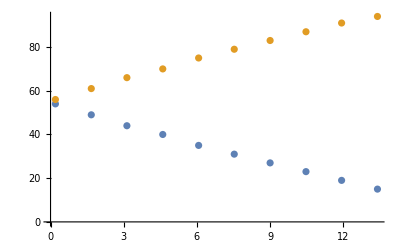

```mathematica
(*Lunghezza sottosistema*)
epsilon=0.001;
OmegaCATS={};
nmin=1;
For[n=1,n<=Length[TIMES],++n,
time=TIMES[[n]];
MatriceCATS=Import[FOLDERCATS~StringJoin~FILENAME~StringJoin~"_t"~StringJoin~ToString[time]~StringJoin~".csv"];
ellLCATS=1+Length[Select[FoldList[Times,1,Table[Sqrt[3-(MatriceCATS[[j,j]]+MatriceCATS[[j+L,j+L]]+MatriceCATS[[j+2L,j+2L]])],{j,1,L}]],#>1-epsilon&]];
ellRCATS=Length[MatriceCATS]/3-Length[Select[FoldList[Times,1,Reverse[Table[Sqrt[3-(MatriceCATS[[j,j]]+MatriceCATS[[j+L,j+L]]+MatriceCATS[[j+2L,j+2L]])],{j,1,L}]]],#>1-epsilon&]];
If[ellLCATS>ellRCATS, Print["Warning for ",n,": nmin has been updated to ", n+1]; nmin=n+1;];
AppendTo[OmegaCATS,{time,ellLCATS,ellRCATS}]
]
ListPlot[{OmegaCATS[[All,{1,2}]],OmegaCATS[[All,{1,3}]]}]
```

## Fisher information

### with just a flip

```mathematica
(*Fisher per unità di lunghezza del sotsistema circa puro*)
FisherFLIPS={};
For[n=nmin,n<=Length[TIMES],++n,
time=TIMES[[n]];
Matrice=Import[FOLDERFLIPS~StringJoin~FILENAME~StringJoin~"_t"~StringJoin~ToString[time]~StringJoin~".csv"];
size=OmegaFLIPS[[n,3]]-OmegaFLIPS[[n,2]]+1;
indices=(Range[OmegaFLIPS[[n,2]],OmegaFLIPS[[n,3]]])~Join~(Range[OmegaFLIPS[[n,2]],OmegaFLIPS[[n,3]]]+L)~Join~(Range[OmegaFLIPS[[n,2]],OmegaFLIPS[[n,3]]]+2 L);
Mat=Matrice[[indices,indices]];
vec0=ConstantArray[1/Sqrt[2](*/Sqrt[2]*),size]~Join~ConstantArray[0/Sqrt[2](*-1/Sqrt[2]*),size]~Join~ConstantArray[1/Sqrt[2],size];
vecpart=Partition[vec0,size];
vec0/=Flatten[ConstantArray[Sqrt[Abs[vecpart[[1]]]^2+Abs[vecpart[[2]]]^2+Abs[vecpart[[3]]]^2],3]];
Dmat=IdentityMatrix[3*size];
Monitor[
While[Norm[vec0.(Mat-Dmat)]>0.01,
vec1=vec0.Mat;
vecpart=Partition[vec1,size];
Dmat=KroneckerProduct[IdentityMatrix[3],DiagonalMatrix[Sqrt[Abs[vecpart[[1]]]^2+Abs[vecpart[[2]]]^2+Abs[vecpart[[3]]]^2]]];
vec0=vec1.Inverse[Dmat];
];
,Refresh[(*Pause[0.03];*){time,Norm[vec0.(Mat-Dmat)]},UpdateInterval->1,TrackedSymbols->{}]];
vecpart=Partition[vec0,size];
Print["Norm=",vec0.(Mat-Dmat)//Norm];
Print["Val=",Total[Diagonal[Dmat]]/3/size];
AppendTo[FisherFLIPS,{size,Total[Diagonal[Dmat]]/3/size}];
]
```

Norm=0.009596976683568814857623

Val=1.2707002343030882619980832

Norm=0.00812804

Val=2.1043642118

Norm=0.

Val=2.0293

Norm=0.

Val=2.2378

Norm=0.01

Val=2.456259

Norm=0.

Val=2.683873

Norm=0.

Val=2.941299

Norm=0.

Val=3.18059

Norm=0.

Val=3.434102

Norm=0.

Val=3.6776029

```mathematica
fitfisherFLIPS=LinearModelFit[FisherFLIPS[[3;;]],{1,x,1/x},x]
fitfisher1FLIPS=a+b E^(-c #)&/.FindFit[FisherFLIPS[[2;;]],a+b E^(-c x),{a,b,{c,0.01},{d,0}},x]
fitfisher2FLIPS=a+b /#+c Log[#]&/.FindFit[FisherFLIPS[[3;;]],a+b /x+c Log[x],{a,b,{c,0.02}},x]
```

FittedModel[0.82406+(«40»)/x+0.032983 x]

1.0695+0.72462 ⅇ^(-(-0.015645) #1)&

-11.114+77.426/#1+3.1298 Log[#1]&

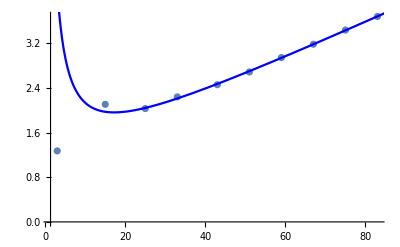

```mathematica
Show[ListPlot[FisherFLIPS,PlotRange->All]
,Plot[fitfisherFLIPS[x],{x,0,200},ColorFunction->Function[{x,y},Blue],PlotRange->All]
(*,Plot[fitfisher1FLIPS[x],{x,0,200},ColorFunction->Function[{x,y},Red]]*)
(*,Plot[fitfisher2FLIPS[x],{x,0,200},ColorFunction->Function[{x,y},Green]]*)
]
```

### 45° rotation

```mathematica
(*Fisher per unità di lunghezza del sotsistema circa puro*)
FisherCATS={};
For[n=nmin,n<=Length[TIMES],++n,
time=TIMES[[n]];
Matrice=Import[FOLDERCATS~StringJoin~FILENAME~StringJoin~"_t"~StringJoin~ToString[time]~StringJoin~".csv"];
size=OmegaCATS[[n,3]]-OmegaCATS[[n,2]]+1;
indices=(Range[OmegaCATS[[n,2]],OmegaCATS[[n,3]]])~Join~(Range[OmegaCATS[[n,2]],OmegaCATS[[n,3]]]+L)~Join~(Range[OmegaCATS[[n,2]],OmegaCATS[[n,3]]]+2 L);
Mat=Matrice[[indices,indices]];
vec0=ConstantArray[1/Sqrt[2](*/Sqrt[2]*),size]~Join~ConstantArray[0/Sqrt[2](*-1/Sqrt[2]*),size]~Join~ConstantArray[1/Sqrt[2],size];
vecpart=Partition[vec0,size];
vec0/=Flatten[ConstantArray[Sqrt[Abs[vecpart[[1]]]^2+Abs[vecpart[[2]]]^2+Abs[vecpart[[3]]]^2],3]];
Dmat=IdentityMatrix[3*size];
Monitor[
While[Norm[vec0.(Mat-Dmat)]>0.01,
vec1=vec0.Mat;
vecpart=Partition[vec1,size];
Dmat=KroneckerProduct[IdentityMatrix[3],DiagonalMatrix[Sqrt[Abs[vecpart[[1]]]^2+Abs[vecpart[[2]]]^2+Abs[vecpart[[3]]]^2]]];
vec0=vec1.Inverse[Dmat];
];
,Refresh[(*Pause[0.03];*){time,Norm[vec0.(Mat-Dmat)]},UpdateInterval->1,TrackedSymbols->{}]];
vecpart=Partition[vec0,size];
Print["Norm=",vec0.(Mat-Dmat)//Norm];
Print["Val=",Total[Diagonal[Dmat]]/3/size];
AppendTo[FisherCATS,{size,Total[Diagonal[Dmat]]/3/size}];
]
```

Norm=0.009236677977892905

Val=1.1765988667162161832

Norm=0.

Val=1.741

Norm=0.01

Val=1.74224

Norm=0.0089744

Val=1.95455231523

Norm=0.009375

Val=2.21997285141

Norm=0.008906

Val=2.5508936484

Norm=0.009389

Val=2.91157418339

Norm=0.

Val=3.2654

Norm=0.

Val=3.65656

Norm=0.01

Val=4.12613987

```mathematica
fitfisherCATS=LinearModelFit[FisherCATS[[3;;]],{1,x,1/x},x]
fitfisher1CATS=a+b E^(-c #)&/.FindFit[FisherCATS[[2;;]],a+b E^(-c x),{a,b,{c,0.01},{d,0}},x]
fitfisher2CATS=a+b /#+c Log[#]&/.FindFit[FisherCATS[[3;;]],a+b /x+c Log[x],{a,b,{c,0.02}},x]
```

FittedModel[-0.79144+(«40»)/x+0.056057 x]

0.9081+0.5493 ⅇ^(-(-0.02216) #1)&

-19.516+129.95/#1+4.9963 Log[#1]&

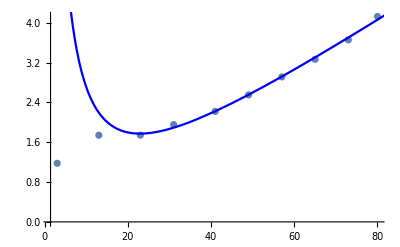

```mathematica
Show[ListPlot[FisherCATS,PlotRange->All]
,Plot[fitfisherCATS[x],{x,0,200},ColorFunction->Function[{x,y},Blue]]
(*,Plot[fitfisher1CATS[x],{x,0,200},ColorFunction->Function[{x,y},Red]]*)
(*,Plot[fitfisher2CATS[x],{x,0,200},ColorFunction->Function[{x,y},Green]]*)
]
```

### Comparison

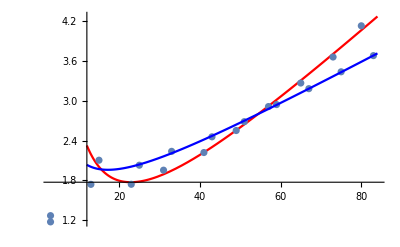

```mathematica
Show[
Plot[fitfisherCATS[x],{x,Min[{OmegaFLIPS[[2,3]]-OmegaFLIPS[[2,2]],OmegaCATS[[2,3]]-OmegaCATS[[2,2]]}],Max[{OmegaFLIPS[[-1,3]]-OmegaFLIPS[[-1,2]],OmegaCATS[[-1,3]]-OmegaCATS[[-1,2]]}]+2},ColorFunction->Function[{x,y},Red],PlotRange->All]
,ListPlot[FisherCATS,PlotRange->All,ColorFunction->Function[{x,y},Red]]
(*,Plot[fitfisher1CATS[x],{x,0,200},ColorFunction->Function[{x,y},Red]]*)
(*,Plot[fitfisher2CATS[x],{x,0,200},ColorFunction->Function[{x,y},Green]]*)

,ListPlot[FisherFLIPS,PlotRange->All,ColorFunction->Function[{x,y},Blue]]
,Plot[fitfisherFLIPS[x],{x,Min[{OmegaFLIPS[[2,3]]-OmegaFLIPS[[2,2]],OmegaCATS[[2,3]]-OmegaCATS[[2,2]]}],Max[{OmegaFLIPS[[-1,3]]-OmegaFLIPS[[-1,2]],OmegaCATS[[-1,3]]-OmegaCATS[[-1,2]]}]+2},ColorFunction->Function[{x,y},Blue],PlotRange->All]
(*,Plot[fitfisher1FLIPS[x],{x,0,200},ColorFunction->Function[{x,y},Red]]*)
(*,Plot[fitfisher2FLIPS[x],{x,0,200},ColorFunction->Function[{x,y},Green]]*)
]
```

I will export the computed Fisher info to make some plots in Julia.

```mathematica
Export[basepath~StringJoin~"/fishers"~StringJoin~FILENAME~StringJoin~"_FLIP.csv",FisherFLIPS];
Export[basepath~StringJoin~"/fishers"~StringJoin~FILENAME~StringJoin~"_CAT.csv",FisherCATS];
```